# Explicit closed form derivatives of Black Scholes formula with respect to volatility

## Black Scholes Option Pricing Formula

```mathematica
x
```

x

```mathematica
Needs["NumericalCalculus`"];
```

```mathematica
normalCDF[d_]:=1/2(1+Erf[d/(√2)]);
logForward[S_,K_,T_,r_]:= Log[S/K]+r*T;
Std[σ_,T_]:= σ √T;
d1[lo_,Z_]:=lo/Z+Z/2;
d2[lo_,Z_]:=lo/Z-Z/2;
BSCall[S_,lo_,Z_]:=S (normalCDF[d1[lo,Z]]-Exp[-lo]normalCDF[d2[lo,Z]]);
BSCallHandy[S_,K_,T_,r_,σ_]:=S normalCDF[d1[logForward[S,K,T,r],Std[σ,T]]]-K Exp[-r T]normalCDF[d2[logForward[S,K,T,r],Std[σ,T]]];

BSPut[S_,lo_,Z_]:=S(-normalCDF[-d1[lo,Z]]+Exp[-lo]normalCDF[-d2[lo,Z]]);
BSPutHandy[S_,K_,T_,r_,σ_]:=-S normalCDF[-d1[logForward[S,K,T,r],Std[σ,T]]]+K Exp[-r T]normalCDF[-d2[logForward[S,K,T,r],Std[σ,T]]];
```

## Priori-checking

```mathematica
D[BSCallHandy[Exp[x],K,T,r,σ],{x,1}]//Simplify
```

1/2 ⅇ^x (1+Erf[(T (2 r+σ^2)+2 Log[ⅇ^x/K])/(2 √2 √T σ)])

```mathematica
dxCall[S_,K_,T_,r_,σ_,q_,l_]:=
S Exp[-q T] normalCDF[d1[logForward[S,K,T,r],Std[σ,T]]]+K Exp[-r T] Exp[-0.5*d2[logForward[S,K,T,r],Std[σ,T]]^2]/(√(2 Pi) σ √T) ∑_(i=0)^(l-2) HermiteH[i,d2[logForward[S,K,T,r],Std[σ,T]]/(√2)]/(- σ √T)^i 2^((- i)/2);
d1x[x_,K_,T_,r_,σ_]:=(x+r T - Log[K]+ (σ^2 T)/2)/(σ √T);

dxCall2[x_,K_,T_,r_,σ_,n_]:=Module[{d1=d1x[x,K,T,r,σ],g},
g=d1/(√2);
Exp[x]/2(1+Erf[g]) + Exp[x] 1/2∑_(j=1)^n Binomial[n,j](√2 σ √T)^-j ((-1)^(j-1) 2/(√Pi) HermiteH[j-1,g] Exp[- g^2])
];
dxCall3[x_,K_,T_,r_,σ_,n_]:=Module[{d1=d1x[x,K,T,r,σ],g},
g=d1/(√2);
Exp[x]/2 (1+∑_(j=0)^n Binomial[n,j] ND[Erf[d1x[xx,K,T,r,σ]/(√2)],{xx,j},x])];
dxCall4[x_,K_,T_,r_,σ_,n_]:=Module[{d1=d1x[x,K,T,r,σ],g},
g=d1/(√2);
Exp[x]/2 (1+∑_(j=0)^n Binomial[n,j] 2/(√Pi) Exp[-g^2] HermiteH[j,g] (σ √(2 T))^-j )];
```

### Check n-the derivative of Erf function: Hermite polynomial

```mathematica
x
```

x

```mathematica
Table[{{HermiteH[n,x],2^(-n/2) HermiteH[n,x/√2]},{D[Erf[x],{x,n+1}],2/(√Pi) Exp[-x^2] HermiteH[n,x]}},{n,0,6,1}]//Simplify
```

{{{1,1},{(2 ⅇ^(-x^2))/(√π),(2 ⅇ^(-x^2))/(√π)}},{{2 x,x},{-(4 ⅇ^(-x^2) x)/(√π),(4 ⅇ^(-x^2) x)/(√π)}},{{-2+4 x^2,-1+x^2},{(ⅇ^(-x^2) (-4+8 x^2))/(√π),(ⅇ^(-x^2) (-4+8 x^2))/(√π)}},{{4 x (-3+2 x^2),x (-3+x^2)},{-(8 ⅇ^(-x^2) x (-3+2 x^2))/(√π),(8 ⅇ^(-x^2) x (-3+2 x^2))/(√π)}},{{4 (3-12 x^2+4 x^4),3-6 x^2+x^4},{(8 ⅇ^(-x^2) (3-12 x^2+4 x^4))/(√π),(8 ⅇ^(-x^2) (3-12 x^2+4 x^4))/(√π)}},{{8 x (15-20 x^2+4 x^4),x (15-10 x^2+x^4)},{-(16 ⅇ^(-x^2) x (15-20 x^2+4 x^4))/(√π),(16 ⅇ^(-x^2) x (15-20 x^2+4 x^4))/(√π)}},{{8 (-15+90 x^2-60 x^4+8 x^6),-15+45 x^2-15 x^4+x^6},{(16 ⅇ^(-x^2) (-15+90 x^2-60 x^4+8 x^6))/(√π),(16 ⅇ^(-x^2) (-15+90 x^2-60 x^4+8 x^6))/(√π)}}}

### Check n-th derivatives of composite function

```mathematica
Module[{S=100,K=100,T=1,r=0.05,σ=0.3,q=0,x,g},
x=Log[S];
g=d1x[x,K,T,r,σ]/(√2);
Table[{
{n,ND[Erf[d1x[xx,K,T,r,σ]/(√2)],{xx,n},x]},
{2/(√Pi) Exp[-g^2] HermiteH[n-1,g](-1)^(n-1)(σ √(2T))^-n,ND[Erf[xx],{xx,n},g](σ √(2T))^-n},
{D[Erf[y],{y,n}],(-1)^(n-1)2/(√Pi) Exp[-y^2] HermiteH[n-1,y] },
{D[Erf[y],{y,n}],(-1)^(n-1)2/(√Pi) Exp[-y^2] HermiteH[n-1,y] }/.y->g,
{(-1)^(n-1)2/(√Pi) Exp[-g^2] HermiteH[n-1,g],
ND[Erf[xx],{xx,n},g]}
},{n,1,10,1}]
]//Simplify
```

{{{1,2.52955},{2.52955,2.52955},{(2 ⅇ^(-y^2))/(√π),(2 ⅇ^(-y^2))/(√π)},{1.0732,1.0732},{1.0732,1.0732}},{{2,-2.67067},{-2.67008,-2.67009},{-(4 ⅇ^(-y^2) y)/(√π),-(4 ⅇ^(-y^2) y)/(√π)},{-0.480615,-0.480615},{-0.480615,-0.480616}},{{3,-25.2503},{-25.2877,-25.2878},{(ⅇ^(-y^2) (-4+8 y^2))/(√π),(ⅇ^(-y^2) (-4+8 y^2))/(√π)},{-1.93116,-1.93116},{-1.93116,-1.93116}},{{4,85.4391},{86.0278,86.0419},{-(8 ⅇ^(-y^2) y (-3+2 y^2))/(√π),-(8 ⅇ^(-y^2) y (-3+2 y^2))/(√π)},{2.7873,2.7873},{2.7873,2.78776}},{{5,741.58},{752.117,751.749},{(8 ⅇ^(-y^2) (3-12 y^2+4 y^4))/(√π),(8 ⅇ^(-y^2) (3-12 y^2+4 y^4))/(√π)},{10.3387,10.3387},{10.3387,10.3337}},{{6,-4130.51},{-4617.36,-4619.94},{-(16 ⅇ^(-y^2) y (15-20 y^2+4 y^4))/(√π),-(16 ⅇ^(-y^2) y (15-20 y^2+4 y^4))/(√π)},{-26.9284,-26.9284},{-26.9284,-26.9435}},{{7,-41826.4},{-36910.4,-36651.},{(16 ⅇ^(-y^2) (-15+90 y^2-60 y^4+8 y^6))/(√π),(16 ⅇ^(-y^2) (-15+90 y^2-60 y^4+8 y^6))/(√π)},{-91.3277,-91.3277},{-91.3277,-90.6858}},{{8,282523.},{346785.,343203.},{-(32 ⅇ^(-y^2) y (-105+210 y^2-84 y^4+8 y^6))/(√π),-(32 ⅇ^(-y^2) y (-105+210 y^2-84 y^4+8 y^6))/(√π)},{364.041,364.041},{364.041,360.281}},{{9,4.62747×10^6},{2.50476×10^6,2.37508×10^6},{(32 ⅇ^(-y^2) (105-840 y^2+840 y^4-224 y^6+16 y^8))/(√π),(32 ⅇ^(-y^2) (105-840 y^2+840 y^4-224 y^6+16 y^8))/(√π)},{1115.56,1115.56},{1115.56,1057.8}},{{10,-4.45878×10^7},{-3.34692×10^7,7.88709×10^7},{-(64 ⅇ^(-y^2) y (945-2520 y^2+1512 y^4-288 y^6+16 y^8))/(√π),-(64 ⅇ^(-y^2) y (945-2520 y^2+1512 y^4-288 y^6+16 y^8))/(√π)},{-6324.24,-6324.24},{-6324.24,14903.2}}}

```mathematica
Module[{S=100,K=100,T=1,r=0.05,σ=0.3,q=0},
Table[{{l,
ND[BSCallHandy[Exp[x],K,T,r,σ],{x,l},Log[100]]}, 
dxCall[S,K,T,r,σ,q,l],
dxCall2[Log[S],K,T,r,σ,l-1],
dxCall3[Log[S],K,T,r,σ,l-1],
dxCall4[Log[S],K,T,r,σ,l-1]
},{l,0,10,1}]
]
With[{S=100,K=100,T=1,r=0.05,σ=0.3,l=2},
{BSCallHandy[S,K,T,r,σ],ND[BSCallHandy[Exp[x],K,T,r,σ],{x,l},Log[100]],dxCall2[Log[S],K,T,r,σ,l-1],dxCall[S,K,T,r,σ,l]}]
```

{{{0,14.2313},62.4252,62.4252,50,50},{{1,62.4252},62.4252,62.4252,62.4252,103.66},{{2,188.905},188.903,188.903,188.903,160.301},{{3,181.66},181.876,181.876,181.847,-319.492},{{4,-1217.43},-1223.04,-1223.04,-1221.26,-3160.64},{{5,-989.894},-988.844,-988.844,-1010.97,5766.73},{{6,43514.},45828.7,45828.7,45173.1,154496.},{{7,70478.9},32819.,32819.,53595.6,-73.3223},{{8,-2.47858×10^6},-2.56743×10^6,-2.56743×10^6,-2.65487×10^6,-1.02966×10^7},{{9,-1.16966×10^7},-1.55566×10^6,-1.55566×10^6,-6.08505×10^6,-2.11557×10^7},{{10,3.04503×10^8},2.0063×10^8,2.0063×10^8,2.70974×10^8,8.71773×10^8}}

{14.2313,188.905,188.903,dxCall[100,100,1,0.05,0.3,2]}

## n-th derivative of option pricing formula

### With respect to x

```mathematica
DxP[x_,K_,T_,r_,σ_,c_,n_]:=Module[{d1=d1x[x,K,T,r,σ],g},
g=c*d1/(√2);
c*Exp[x]/2(1+Erf[g]) + c*Exp[x] 1/2∑_(j=1)^(n-1) Binomial[n-1,j](c*√2 σ √T)^-j ((-1)^(j-1) 2/(√Pi) HermiteH[j-1,g] Exp[- g^2])
];
NDxP[x_,K_,T_,r_,σ_,c_,n_]:=If[c==1, ND[BSCallHandy[Exp[xx],K,T,r,σ],{xx,n},x],
 ND[BSPutHandy[Exp[xx],K,T,r,σ],{xx,n},x]];
```

```mathematica
With[{x=Log[100],K=100,T=1,r=0.05,σ=0.3},
Table[{DxP[x,K,T,r,σ,c,n],NDxP[x,K,T,r,σ,c,n]}, {n,1,4,1},{c,-1,1,2}]]//MatrixForm
```

((-37.5748
-37.5748) | (62.4252
62.4252)
(88.9028
88.9047) | (188.903
188.905)
(81.8763
81.6601) | (181.876
181.66)
(-1323.04
-1317.43) | (-1223.04
-1217.43))

### With respect to volatility

```mathematica
Table[BellY[n,n-1,{x,y}],{n,2,10,1}]
```

{y,3 x y,6 x^2 y,10 x^3 y,15 x^4 y,21 x^5 y,28 x^6 y,36 x^7 y,45 x^8 y}

```mathematica
DvV[x_,K_,T_,r_,σ_,c_,n_]:=∑_(k=1)^n (n!)/((2k-n)! (n-k)!) (T^k σ^(2k-n))/2^(n-k)∑_(j=0)^k Binomial[k,j] (-1)^(k-j)DxP[x,K,T,r,σ,c,k+j];

NDvV[x_,K_,T_,r_,σ_,c_,n_]:=If[c==1, ND[BSCallHandy[Exp[x],K,T,r,xx],{xx,n},σ],
 ND[BSPutHandy[Exp[x],K,T,r,xx],{xx,n},σ]];
```

### Comparison with numerical method, we can see the numerical one bear some error in high order cases

```mathematica
With[{x=Log[100],K=100,T=1,r=0.05,σ=0.3},
Table[{DvV[x,K,T,r,σ,c,n],NDvV[x,K,T,r,σ,c,n]}, {n,1,5,1},{c,-1,1,2}]]//MatrixForm
```

((37.9433
37.9433) | (37.9433
37.9433)
(0.667521
0.661521) | (0.667521
0.661521)
(-44.6068
-44.1638) | (-44.6068
-44.1638)
(466.081
444.237) | (466.081
444.237)
(-7616.98
-6721.4) | (-7616.98
-6721.4))

### Taylor series coefficients comparison

```mathematica
With[{x=Log[100],K=100,T=1,r=0.05,σ=0.3},
Table[{DvV[x,K,T,r,σ,c,n]/(n!),NDvV[x,K,T,r,σ,c,n]/(n!)}, {n,1,10,1},{c,-1,1,2}]]//MatrixForm
```

((37.9433
37.9433) | (37.9433
37.9433)
(0.33376
0.33076) | (0.33376
0.33076)
(-7.43446
-7.36064) | (-7.43446
-7.36064)
(19.42
18.5099) | (19.42
18.5099)
(-63.4748
-56.0117) | (-63.4748
-56.0117)
(208.285
161.518) | (208.285
161.518)
(-681.132
-438.26) | (-681.132
-438.261)
(2221.53
1120.2) | (2221.53
1120.23)
(-7225.8
-2705.) | (-7225.8
-2705.43)
(23436.1
6192.47) | (23436.1
6198.21))

### Exactly what we got from Taylor series

```mathematica
With[{x=Log[100],K=100,T=1,r=0.05},Series[BSCallHandy[Exp[x],K,T,r,σ],{σ,0.3,10}]]
```

14.2313+37.9433 (σ-0.3)+0.33376 (σ-0.3)^2-7.43446 (σ-0.3)^3+19.42 (σ-0.3)^4-63.4748 (σ-0.3)^5+208.285 (σ-0.3)^6-681.132 (σ-0.3)^7+2221.53 (σ-0.3)^8-7225.8 (σ-0.3)^9+23436.1 (σ-0.3)^10+O[σ-0.3]^11

## Visualize the function

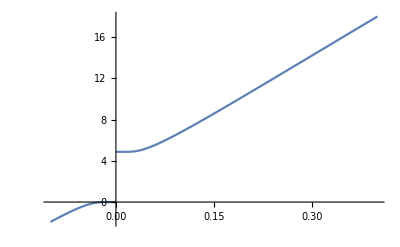

```mathematica
With[{S=100,K=100,T=1,r=0.05},
Plot[BSCallHandy[S,K,T,r,x],{x,-0.1,0.4}]]
```

```mathematica
f[z_]:=With[{S=100,K=100,T=1,r=0.05},
BSCallHandy[S,K,T,r,σ]]/.σ->z;
f2[z_]:=With[{x=Log[100],K=100,T=1,r=0.05},Normal[Series[BSCallHandy[Exp[x],K,T,r,σ],{σ,0.3,10}]]]/.σ->z
u[{x_,y_}]:=Re[f[x+I y]];
v[{x_,y_}]:=Im[f[x+I y]];
Φ[{x_,y_}]:={u[{x,y}],v[{x,y}]};
Φ̄[{x_,y_}]:={u[{x,y}],-v[{x,y}]};
SuperStar[Φ][{x_,y_}]:={v[{x,y}],u[{x,y}]};
u2[{x_,y_}]:=Re[f2[x+I y]];
v2[{x_,y_}]:=Im[f2[x+I y]];
```

```mathematica
Plot3D[{u[{x,y}],v[{x,y}]},{x,-0.0,0.1},{y,-0.1,0.1},MeshFunctions->{#3&},Mesh->15]
Plot3D[{u2[{x,y}],v2[{x,y}]},{x,-0.0,0.1},{y,-0.1,0.1},MeshFunctions->{#3&},Mesh->15]
```

-Graphics3D-

-Graphics3D-

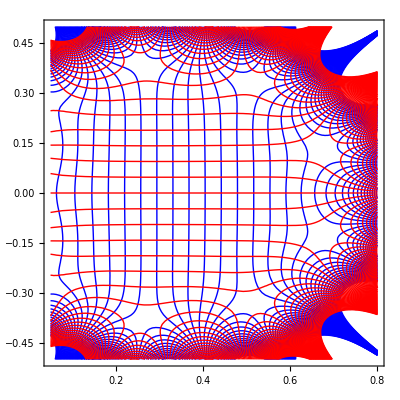

```mathematica
Show[ContourPlot[u2[{x, y}], {x, 0.05, 0.8}, {y, -0.5, 0.5},Contours->50,ContourStyle->{Blue},ContourShading -> None] ,
 ContourPlot[v2[{x, y}], {x, 0.05, 0.8}, {y, -0.5, 0.5},Contours->50,ContourStyle->{Red} ,ContourShading -> None]]
```

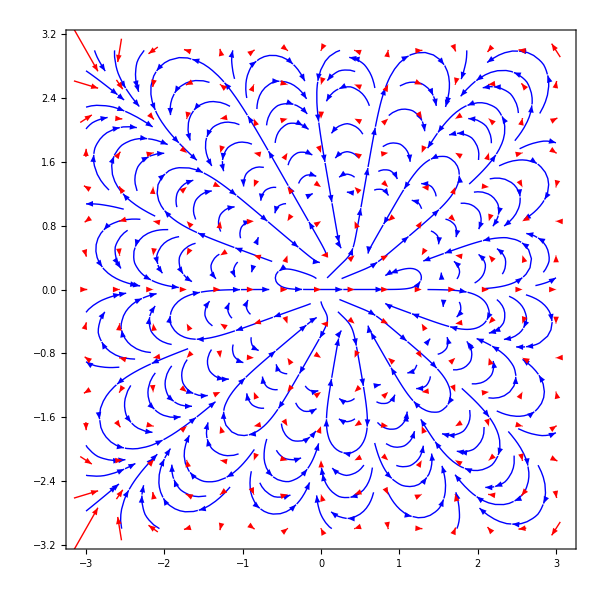

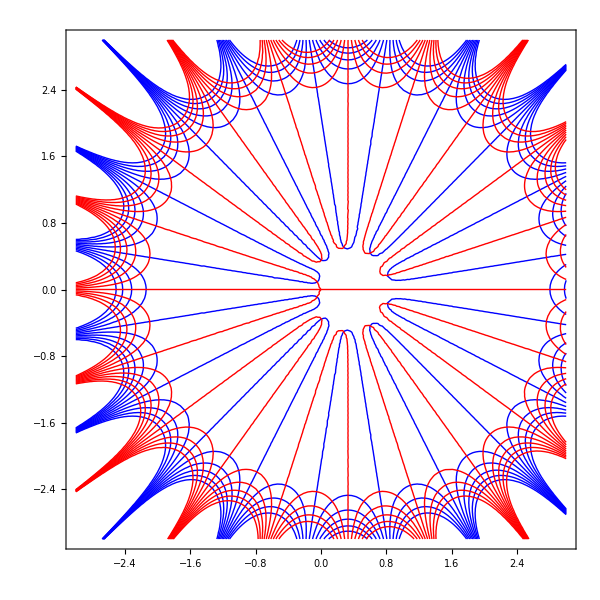

Show::gcomb: Could not combine the graphics objects in Show[StreamPlot[Φ̄[{x,y}],{x,-3,3},{y,-3,3},StreamStyle→Blue],VectorPlot[Φ̄[{x,y}],{x,-3,3},{y,-3,3},VectorStyle→Red],ImageSize→600].

```mathematica
Show[StreamPlot[{u2[{x,y}],v2[{x,y}]},{x,-3,3},{y,-3,3},StreamStyle->Blue],
	VectorPlot[{u2[{x,y}],v2[{x,y}]},{x,-3,3},{y,-3,3},VectorStyle->Red],ImageSize->600]
Show[ContourPlot[u2[{x, y}], {x, -3, 3}, {y, -3, 3},Contours->10,ContourStyle->{Blue},ContourShading -> None] ,
 ContourPlot[v2[{x, y}], {x, -3, 3}, {y, -3, 3},Contours->10,ContourStyle->{Red} ,ContourShading -> None]]
```

## Explicit inversion series of the implied volatility

```mathematica
x
```

x

```mathematica
With[{n=7},SeriesData[x,0,Array[a,n],1,n+1,1]]
With[{n=7},CoefficientList[InverseSeries[SeriesData[x,0,Array[a,n],1,n+1,1]],x]]
```

a[1] x+a[2] x^2+a[3] x^3+a[4] x^4+a[5] x^5+a[6] x^6+a[7] x^7+O[x]^8

{0,1/a[1],-a[2]/a[1]^3,(2 a[2]^2-a[1] a[3])/a[1]^5,(-5 a[2]^3+5 a[1] a[2] a[3]-a[1]^2 a[4])/a[1]^7,(14 a[2]^4-21 a[1] a[2]^2 a[3]+3 a[1]^2 a[3]^2+6 a[1]^2 a[2] a[4]-a[1]^3 a[5])/a[1]^9,(-42 a[2]^5+84 a[1] a[2]^3 a[3]-28 a[1]^2 a[2] a[3]^2-28 a[1]^2 a[2]^2 a[4]+7 a[1]^3 a[3] a[4]+7 a[1]^3 a[2] a[5]-a[1]^4 a[6])/a[1]^11,1/a[1]^13(132 a[2]^6-330 a[1] a[2]^4 a[3]+180 a[1]^2 a[2]^2 a[3]^2-12 a[1]^3 a[3]^3+120 a[1]^2 a[2]^3 a[4]-72 a[1]^3 a[2] a[3] a[4]+4 a[1]^4 a[4]^2-36 a[1]^3 a[2]^2 a[5]+8 a[1]^4 a[3] a[5]+8 a[1]^4 a[2] a[6]-a[1]^5 a[7])}

```mathematica
With[{x=Log[100],K=100,T=1,r=0.05,fixVol=0.3,c=1},
fArray:=k↦Table[DvV[x,K,T,r,fixVol,c,j],{j,1,k}];
fArray:=k↦Table[DvV[x,K,T,r,fixVol,c,j+1]/((j+1) DvV[x,K,T,r,fixVol,c,1]),{j,1,k}];
fArray@5
]
```

{0.0087963,-0.391872,3.07091,-40.1493,658.726}

```mathematica
x
```

x

```mathematica
DpV[S_,K_,T_,r_,c_,Price_,fixVol_,n_]:=Module[{x,z,f,fHat,fHatArray,g},
x=Log[S];
z=If[c==1,Price - BSCallHandy[S,K,T,r,fixVol],Price-BSPutHandy[S,K,T,r,fixVol]];
f:=k↦DvV[x,K,T,r,fixVol,c,k];
fHat:=k↦f[k+1]/((k+1) f[1]);
fHatArray:=k↦Table[fHat[j],{j,1,k}];
g = Which[
n==0,0,
n==1,1/f[1],
n≥2, 1/f[1]^n∑_(k=1)^(n-1) (-1)^k ((n+k-1)!)/((n-1)!) BellY[n-1,k,fHatArray[n-k]]];
g
];
Module[{x=Log[100],S=100,K=100,T=1,r=0.05,σ=0.3,fixVol=0.2,c=1,n=7,truePrice,fixPrice,dpVArray,vol,gk},
truePrice = If[c==1,BSCallHandy[S,K,T,r,σ],BSPutHandy[S,K,T,r,σ]];
fixPrice = If[c==1,BSCallHandy[S,K,T,r,fixVol],BSPutHandy[S,K,T,r,fixVol]];
dpVArray = Table[DpV[S,K,T,r,c,truePrice,fixVol,j],{j,1,n}];
gk=k↦DpV[S,K,T,r,c,truePrice,fixVol,k];
vol =fixVol+ ∑_(k=1)^n gk[k]/(k!) (truePrice-fixPrice)^k]
```

0.300028

```mathematica
VolOfPrice[S_,K_,T_,r_,price_,c_,fixVol_,n_]:=Module[{x=Log[S],truePrice=price,fixPrice,dpVArray,vol,gk},
fixPrice = If[c==1,BSCallHandy[S,K,T,r,fixVol],BSPutHandy[S,K,T,r,fixVol]];
dpVArray = Table[DpV[S,K,T,r,c,truePrice,fixVol,j],{j,1,n}];
gk=k↦DpV[S,K,T,r,c,truePrice,fixVol,k];
vol =fixVol+ ∑_(k=1)^n gk[k]/(k!) (truePrice-fixPrice)^k];
```

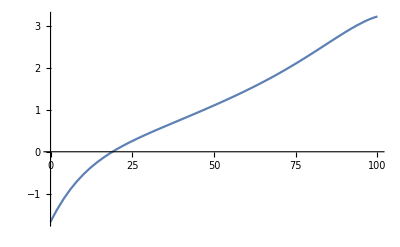
{-Graphics-,26.4621}

```mathematica
Module[{S=100,K=80,T=1,r=0.05,trueVol=0.3,truePrice,volEstimation},
{Plot[VolOfPrice[S,K,T,r,x,1,1,6],{x,0,100}]
,BSCallHandy[S,K,T,r,trueVol]}
]
```

```mathematica
Module[{S=100,K=80,T=1,r=0.05,trueVol=0.3,truePrice,volEstimation},
truePrice = BSCallHandy[S,K,T,r,trueVol];
Table[volEstimation=VolOfPrice[S,K,T,r,truePrice,1,fixVol,n],{fixVol,0.05,1,0.1},{n,5,10,3}]//MatrixForm
]
```

(1.66033×10^37 | -3.06428×10^61
934.655 | -1.2702×10^6
0.300238 | 0.299955
0.300006 | 0.3
0.300507 | 0.300068
0.302221 | 0.300537
0.304854 | 0.301564
0.307951 | 0.303045
0.311188 | 0.304822
0.314327 | 0.30677)

```mathematica
K
$ContextPath
2.343324235424321`3
Context[K]
```

K

{NumericalCalculus`,CloudObjectLoader`,SymbolicMachineLearningLoader`,IconizeLoader`,HTTPHandlingLoader`,StreamingLoader`,PacletManager`,System`,Global`}

2.34

System`

```mathematica
Manipulate[
Module[{targetCallPrice,estimatedCallPrice,estimatedIV,newtonRoot},

targetCallPrice=BSCallHandy[S,K,T,r,σ];
estimatedIV=VolOfPrice[S,K,T,r,targetCallPrice,1,a,order];
newtonRoot = Timing[FindRoot[BSCallHandy[S,K,T,r,xx]==targetCallPrice,{xx,a}]];

{{targetCallPrice},{σ,estimatedIV,newtonRoot}}],
"underlying, S_0",
{{S,100.,""},0,150,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"strike, K",
{{K,100,""},0,150,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"volatility, σ",
{{σ,0.3,""},0.01,1,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"risk-free rate, r",
{{r,0.05,""},0.0,0.25,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"years to maturity, T",
{{T,1,""},0.1,3,0.25,Appearance->"Labeled", ImageSize-> Tiny},
"",
"truncated order, order",
{{order,5,""},0,20,5,Appearance->"Labeled", ImageSize-> Tiny},
"",
"fixed volatility, a",
{{a,0.3,""},0.05,1,0.1,Appearance->"Labeled", ImageSize-> Tiny},

ControlPlacement->Left,SaveDefinitions->True
]
```

## Error Analysis

```mathematica
LogVolError[fixVol_,K_,n_]:=Module[{x=Log[100],S=100,T=1,r=0.05,σ=0.3,c=1,truePrice,fixPrice,dpVArray,vol,gk},
truePrice = If[c==1,BSCallHandy[S,K,T,r,σ],BSPutHandy[S,K,T,r,σ]];
fixPrice = If[c==1,BSCallHandy[S,K,T,r,fixVol],BSPutHandy[S,K,T,r,fixVol]];
dpVArray = Table[DpV[S,K,T,r,c,truePrice,fixVol,j],{j,1,n}];
gk=k↦DpV[S,K,T,r,c,truePrice,fixVol,k];
vol =fixVol+ ∑_(k=1)^n gk[k]/(k!) (truePrice-fixPrice)^k;
{fixVol,Log[10,Abs[vol-σ]]}];
```

```mathematica
LogVolErrorPlot[fixVol_,K_,title_]:=Module[{logError2,logError4,logError8,fit2,fit4,fit8,plot2,plot4,plot8,listPlot2,listPlot4,listPlot8},

logError2 = Table[LogVolError[a,K,2],{a,0.1,1,0.05}];
fit2=Interpolation[logError2,InterpolationOrder->3];
plot2 = Plot[fit2[x],{x,0.1,1},PlotRange->{Full,{-17,3}},PlotStyle->Brown];
listPlot2 = ListPlot[logError2,PlotRange->{Full,{-17,3}},PlotMarkers->{●,10}];

logError4 = Table[LogVolError[a,K,4],{a,0.1,1,0.05}];
fit4=Interpolation[logError4,InterpolationOrder->3];
plot4 = Plot[fit4[x],{x,0.1,1},PlotRange->{Full,{-17,3}},PlotStyle->Orange];
listPlot4 = ListPlot[logError4,PlotRange->{Full,{-17,3}},PlotMarkers->{▲,10}];

logError8 = Table[LogVolError[a,K,8],{a,0.1,1,0.05}];
fit8=Interpolation[logError8,InterpolationOrder->3];
plot8 = Plot[fit8[x],{x,0.1,1},PlotRange->{Full,{-17,3}},PlotStyle->Blue];
listPlot8 = ListPlot[logError8,PlotRange->{Full,{-17,3}},PlotMarkers->{■,10}];

CellPrint[{Cell["Data","Subsubsection"],
Cell[BoxData[ToBoxes[logError2]],"Output"],
Cell[BoxData[ToBoxes[logError4]],"Output"],
Cell[BoxData[ToBoxes[logError8]],"Output"],
Cell["Plot","Subsubsection"],
Cell[BoxData[ToBoxes[
Show[plot2,listPlot2,plot4,listPlot4,plot8,listPlot8,
AxesLabel->{HoldForm[initial point],HoldForm[log error]},PlotLabel->HoldForm[title],LabelStyle->{GrayLevel[0]}]]],"Output"]}]

]
LogVolErrorPlot[0.3,100,"ddd"]
```

#### Data

{{0.1,-1.38213},{0.15,-2.33278},{0.2,-3.2373},{0.25,-4.41045},{0.3,-15.9546},{0.35,-4.75995},{0.4,-3.96759},{0.45,-3.52046},{0.5,-3.20417},{0.55,-2.95479},{0.6,-2.7456},{0.65,-2.56327},{0.7,-2.40033},{0.75,-2.25218},{0.8,-2.11578},{0.85,-1.98899},{0.9,-1.87024},{0.95,-1.75833},{1.,-1.65233}}

{{0.1,-0.528658},{0.15,-2.23008},{0.2,-3.80735},{0.25,-5.8314},{0.3,-15.9546},{0.35,-6.59192},{0.4,-5.38272},{0.45,-4.75988},{0.5,-4.36151},{0.55,-4.07624},{0.6,-3.85493},{0.65,-3.67115},{0.7,-3.5088},{0.75,-3.35737},{0.8,-3.21},{0.85,-3.0626},{0.9,-2.91326},{0.95,-2.7616},{1.,-2.60824}}

{{0.1,1.43357},{0.15,-1.84584},{0.2,-4.78427},{0.25,-8.48098},{0.3,-15.9546},{0.35,-9.90453},{0.4,-7.74575},{0.45,-6.64185},{0.5,-5.94469},{0.55,-5.45713},{0.6,-5.09433},{0.65,-4.81262},{0.7,-4.58678},{0.75,-4.40091},{0.8,-4.24408},{0.85,-4.10793},{0.9,-3.98508},{0.95,-3.86789},{1.,-3.74757}}

#### Plot

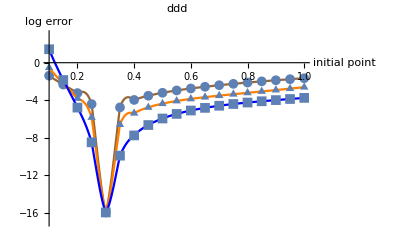

#### ATM

{62.4252,1.99818,1.08654,1.19378,0.81213,0.960465,0.796877,0.831225,0.731277,0.744952,0.675824,0.68173,0.630361,0.632684,0.592651,0.593132,0.560849,0.560321,0.533611,0.532512}

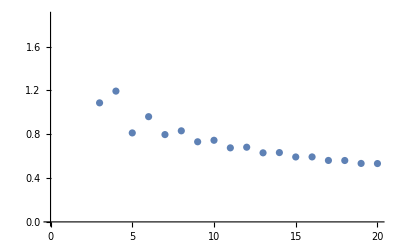

```mathematica
dxPArray1=Module[{S=100,K=100,T=1,r=0.05,σ=0.3,fixVol=0.3,c=1,price,dxP},
price = BSCallHandy[S,K,T,r,σ];
dxP :=n↦DxP[Log[S],K,T,r,σ,c,n];

Table[Abs[dxP[n]/n!]^(1/n),{n,1,100,5}]
]
ListPlot[dxPArray1]
```

```mathematica
LogVolErrorPlot[0.3,100,"ATM log error"]
```

#### Data

{{0.1,-1.38213},{0.15,-2.33278},{0.2,-3.2373},{0.25,-4.41045},{0.3,-15.9546},{0.35,-4.75995},{0.4,-3.96759},{0.45,-3.52046},{0.5,-3.20417},{0.55,-2.95479},{0.6,-2.7456},{0.65,-2.56327},{0.7,-2.40033},{0.75,-2.25218},{0.8,-2.11578},{0.85,-1.98899},{0.9,-1.87024},{0.95,-1.75833},{1.,-1.65233}}

{{0.1,-0.528658},{0.15,-2.23008},{0.2,-3.80735},{0.25,-5.8314},{0.3,-15.9546},{0.35,-6.59192},{0.4,-5.38272},{0.45,-4.75988},{0.5,-4.36151},{0.55,-4.07624},{0.6,-3.85493},{0.65,-3.67115},{0.7,-3.5088},{0.75,-3.35737},{0.8,-3.21},{0.85,-3.0626},{0.9,-2.91326},{0.95,-2.7616},{1.,-2.60824}}

{{0.1,1.43357},{0.15,-1.84584},{0.2,-4.78427},{0.25,-8.48098},{0.3,-15.9546},{0.35,-9.90453},{0.4,-7.74575},{0.45,-6.64185},{0.5,-5.94469},{0.55,-5.45713},{0.6,-5.09433},{0.65,-4.81262},{0.7,-4.58678},{0.75,-4.40091},{0.8,-4.24408},{0.85,-4.10793},{0.9,-3.98508},{0.95,-3.86789},{1.,-3.74757}}

#### Plot

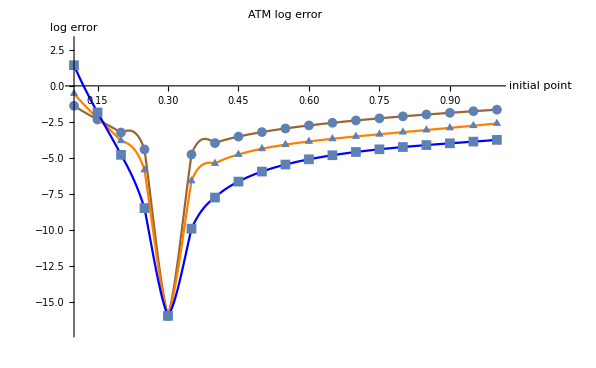

#### ITM

{93.3913,1.67558,1.2371,1.03691,1.01325,0.931296,0.823336,0.808007,0.769617,0.701813,0.698792,0.670938,0.629732,0.625638,0.600689,0.583531,0.570655,0.536156,0.541196,0.526066}

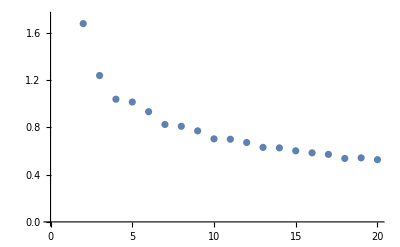

```mathematica
dxPArray2=Module[{S=100,K=70,T=1,r=0.05,σ=0.3,fixVol=0.3,c=1,price,dxP},
price = BSCallHandy[S,K,T,r,σ];
dxP :=n↦DxP[Log[S],K,T,r,σ,c,n];

Table[Abs[dxP[n]/n!]^(1/n),{n,1,100,5}]
]
ListPlot[dxPArray2]
```

```mathematica
LogVolErrorPlot[0.3,55,"ITM log error"]
```

#### Data

{{0.1,15.7722},{0.15,5.11882},{0.2,1.16532},{0.25,-1.15424},{0.3,-16.2556},{0.35,-2.33178},{0.4,-1.75149},{0.45,-1.47285},{0.5,-1.30147},{0.55,-1.18251},{0.6,-1.09371},{0.65,-1.02411},{0.7,-0.967564},{0.75,-0.92034},{0.8,-0.87999},{0.85,-0.844824},{0.9,-0.813619},{0.95,-0.785455},{1.,-0.759611}}

{{0.1,34.2026},{0.15,12.4092},{0.2,4.20777},{0.25,-0.433714},{0.3,-16.2556},{0.35,-2.98504},{0.4,-2.14675},{0.45,-1.77062},{0.5,-1.54979},{0.55,-1.40153},{0.6,-1.29358},{0.65,-1.21061},{0.7,-1.14432},{0.75,-1.08982},{0.8,-1.04398},{0.85,-1.00475},{0.9,-0.970658},{0.95,-0.940665},{1.,-0.913975}}

{{0.1,71.3897},{0.15,27.3408},{0.2,10.6567},{0.25,1.32537},{0.3,-16.2556},{0.35,-4.08581},{0.4,-2.75915},{0.45,-2.20523},{0.5,-1.89686},{0.55,-1.69794},{0.6,-1.55747},{0.65,-1.45206},{0.7,-1.36943},{0.75,-1.30252},{0.8,-1.24697},{0.85,-1.19993},{0.9,-1.15946},{0.95,-1.12417},{1.,-1.09306}}

#### Plot

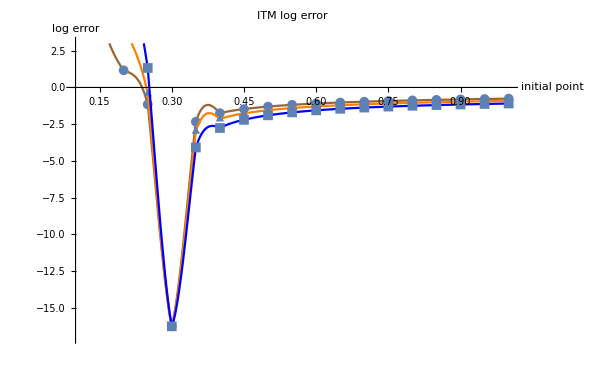

#### OTM

{28.8463,1.74511,1.31951,1.19909,1.03924,0.930078,0.890805,0.810212,0.780473,0.744039,0.690641,0.68272,0.645852,0.631387,0.610578,0.586794,0.576523,0.543048,0.546147,0.529078}

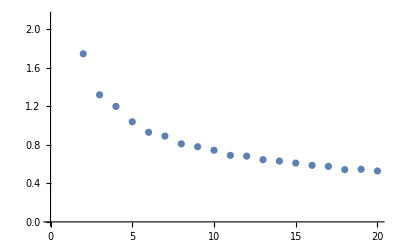

```mathematica
dxPArray3=Module[{S=100,K=130,T=1,r=0.05,σ=0.3,fixVol=0.3,c=1,price,dxP},
price = BSCallHandy[S,K,T,r,σ];
dxP :=n↦DxP[Log[S],K,T,r,σ,c,n];

Table[Abs[dxP[n]/n!]^(1/n),{n,1,100,5}]
]
ListPlot[dxPArray3]
```

```mathematica
LogVolErrorPlot[0.3,145,"OTM log error"]
```

#### Data

{{0.1,3.67067},{0.15,0.574124},{0.2,-0.995159},{0.25,-2.47203},{0.3,-15.6536},{0.35,-3.14422},{0.4,-2.47003},{0.45,-2.13175},{0.5,-1.9191},{0.55,-1.76952},{0.6,-1.6565},{0.65,-1.56659},{0.7,-1.49206},{0.75,-1.42807},{0.8,-1.37142},{0.85,-1.31986},{0.9,-1.27176},{0.95,-1.22588},{1.,-1.18129}}

{{0.1,9.48971},{0.15,2.95963},{0.2,-0.20843},{0.25,-2.94211},{0.3,-15.6536},{0.35,-4.32152},{0.4,-3.26955},{0.45,-2.7595},{0.5,-2.44762},{0.55,-2.23366},{0.6,-2.07613},{0.65,-1.9544},{0.7,-1.85693},{0.75,-1.77667},{0.8,-1.70905},{0.85,-1.65087},{0.9,-1.59981},{0.95,-1.55405},{1.,-1.51211}}

{{0.1,21.5044},{0.15,8.12151},{0.2,1.71613},{0.25,-3.57646},{0.3,-15.6536},{0.35,-6.43231},{0.4,-4.6448},{0.45,-3.80635},{0.5,-3.30715},{0.55,-2.97206},{0.6,-2.72977},{0.65,-2.54537},{0.7,-2.3997},{0.75,-2.28129},{0.8,-2.18287},{0.85,-2.09956},{0.9,-2.02799},{0.95,-1.96572},{1.,-1.91092}}

#### Plot

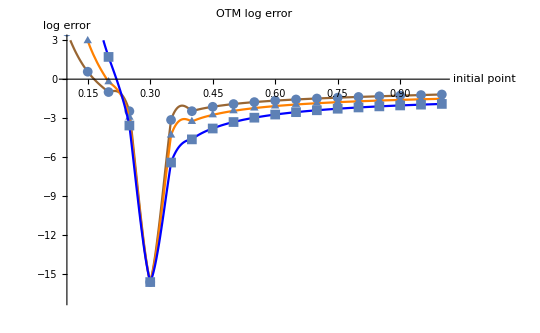

```mathematica
LogVolError[0.30,100]
```

{0.3,Indeterminate}

### Check the Convergence in a numerical way

{0.0263551,0.0358216,0.0556036,0.0662666,0.0730223}

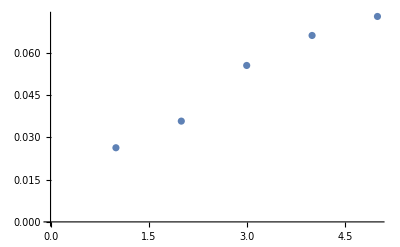

```mathematica
dpVArray1 = Module[{S=100,K=100,T=1,r=0.05,σ=0.3,fixVol=0.3,c=1,price,dpV},
price = BSCallHandy[S,K,T,r,σ];
dpV =n↦DpV[S,K,T,r,c,price,fixVol,n];
Table[Abs[dpV[n]/n!]^(1/n),{n,1,25,5}]
]
ListPlot[dpVArray1]
```

{{0.0291593,0.166106,0.258798,0.311654,0.345826},{0.0266496,0.0599408,0.0922789,0.110148,0.1216},{0.0263551,0.0358216,0.0556036,0.0662666,0.0730223},{0.0264257,0.0252822,0.0397195,0.0473939,0.0522027},{0.0266496,0.0193971,0.0308763,0.0369269,0.0406865},{0.0269773,0.015589,0.0252567,0.0302859,0.033393},{0.027394,0.0126963,0.0213821,0.0257067,0.0283694},{0.0278958,0.00932367,0.0185651,0.0223658,0.0247065},{0.0284833,0.0101212,0.0164725,0.019826,0.0219236},{0.0291593,0.0115519,0.015044,0.0178218,0.0197438}}

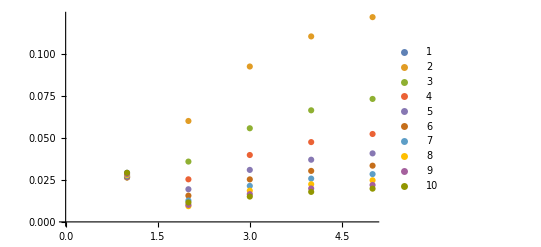

```mathematica
dpVArray2 = Module[{S=100,K=100,T=1,r=0.05,σ=0.3,c=1,price,dpV},
price = BSCallHandy[S,K,T,r,σ];
dpV ={n,fixVol}↦DpV[S,K,T,r,c,price,fixVol,n];
Table[Table[Abs[dpV[n,v]/n!]^(1/n),{n,1,25,5}],{v,0.1,1,0.1}]
]
ListPlot[dpVArray2,PlotLegends->Automatic]
```

```mathematica
dpVArray = Module[{S=100,K=100,T=1,r=0.05,σ=0.3,c=1,price,dpV},
price = BSCallHandy[S,K,T,r,σ];
dpV ={n,fixVol}↦DpV[S,K,T,r,c,price,fixVol,n];
Table[Table[Abs[dpV[n,v]/n!]^(1/n),{n,1,25,5}],{v,1,2,0.2}]
]
```

{{0.0291593,0.0115519,0.015044,0.0178218,0.0197438},{0.0307962,0.0133264,0.014828,0.0145154,0.0168392},{0.0328569,0.0151257,0.0165906,0.0174318,0.0180171},{0.0354106,0.0172417,0.0189107,0.0199015,0.020555},{0.0385482,0.019793,0.021735,0.022886,0.023643},{0.0423868,0.0228967,0.0251788,0.0265255,0.0274098}}

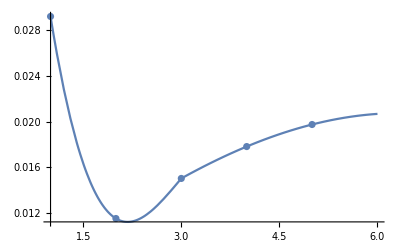

```mathematica
f=Interpolation[dpVArray[[1]]];
Show[Plot[f[x],{x,1,6}],ListPlot[dpVArray[[1]]]]
```

```mathematica
dpVArray = Module[{S=100,K=100,T=1,r=0.05,σ=0.3,c=1,price,dpV},
price = BSCallHandy[S,K,T,r,σ];
dpV ={n,fixVol}↦DpV[S,K,T,r,c,price,fixVol,n];
Table[Table[Abs[dpV[n,v]/n!]^(1/n),{n,1,25,5}],{v,5,15,5}]
]
```

{{0.584978,0.556777,0.627666,0.666911,0.692076},{6896.58,11172.1,13071.2,14072.8,14701.3},{4.22635×10^10,1.39651×10^11,1.3378×10^11,2.24407×10^11,2.44797×10^11}}

## Invert the log stock price

```mathematica
x
```

x

```mathematica
With[{K=100,T=1,r=0.05,σ=0.3},
Table[DxP[Log[K*Exp[-r T]],K,T,r,σ,1,n],{n,1,10}]]
```

{53.2325,178.313,240.853,-1117.66,-3186.69,41062.4,155144.,-2.2461×10^6,-1.10522×10^7,1.71308×10^8}

```mathematica
Module[{K=100,T=1,r=0.05,σ=0.3},
Series[BSCallHandy[Exp[xx],K,T,r,σ],{xx,Log[K],10}]]
```

14.2313+62.4252 (xx-Log[100])+94.4514 (xx-Log[100])^2+30.3127 (xx-Log[100])^3-50.96 (xx-Log[100])^4-8.24037 (xx-Log[100])^5+63.651 (xx-Log[100])^6+6.51171 (xx-Log[100])^7-63.6764 (xx-Log[100])^8-4.28699 (xx-Log[100])^9+55.2882 (xx-Log[100])^10+O[xx-Log[100]]^11

```mathematica
InverseSeries[%]
```

Log[100]+0.0160192 (xx-14.2313)-0.000388266 (xx-14.2313)^2+0.0000168251 (xx-14.2313)^3-8.44791×10^-7 (xx-14.2313)^4+4.58395×10^-8 (xx-14.2313)^5-2.61262×10^-9 (xx-14.2313)^6+1.53975×10^-10 (xx-14.2313)^7-9.2973×10^-12 (xx-14.2313)^8+5.71812×10^-13 (xx-14.2313)^9-3.56793×10^-14 (xx-14.2313)^10+O[xx-14.2313]^11

### with respect to S

```mathematica
Manipulate[
Module[{targetCallPrice,SeriesX,estimatedX,newtonRoot},

SeriesX = Series[BSCallHandy[xx,K,T,r,σ],{xx,a,order}];
seriesTable = Table[
{S,
Normal[SeriesX]/.xx->S ,
BSCallHandy[S,K,T,r,σ]},
{S,1,3 K,10}];
estimatedX=Normal[InverseSeries[SeriesX]]/.xx->K2;
estimatedPrice = BSCallHandy[estimatedX,K,T,r,σ];
newtonRoot = Timing[FindRoot[BSCallHandy[xx,K,T,r,σ]==K2,{xx,K}]];

{{K2,(*estimatedPrice,*)estimatedX,newtonRoot},seriesTable}
],
"underlying, K2",
{{K2,20,""},0,100,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"strike, K",
{{K,100,""},0,150,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"volatility, σ",
{{σ,0.3,""},0.01,1,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"risk-free rate, r",
{{r,0.05,""},0.0,0.25,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"years to maturity, T",
{{T,1,""},0.1,3,0.25,Appearance->"Labeled", ImageSize-> Tiny},
"",
"truncated order, order",
{{order,5,""},0,100,5,Appearance->"Labeled", ImageSize-> Tiny},
"",
"fixed volatility, a",
{{a,100,""},0,300,1,Appearance->"Labeled", ImageSize-> Tiny},

ControlPlacement->Left,SaveDefinitions->True
]
```

#### We see the convergent radius equals to fixS and divergent beyond (0, 2 fixS). So we consider the expansion with respect to Log[S], and it should be a more feasible choice.

### with respect to logS

```mathematica
With[{x=Log[100],K=100,T=1,r=0.05,σ=0.3,c=1,n=10},
Table[DxP[x,K,T,r,σ,c,k]/k!,{k,1,n}]]
```

{62.4252,94.4514,30.3127,-50.96,-8.24037,63.651,6.51171,-63.6764,-4.28699,55.2882}

```mathematica
Module[{S=100,K=100,T=1,r=0.05,σ=0.3},
Series[BSCallHandy[Exp[xx],K,T,r,σ],{xx,Log[100],10}]]
```

14.2313+62.4252 (xx-Log[100])+94.4514 (xx-Log[100])^2+30.3127 (xx-Log[100])^3-50.96 (xx-Log[100])^4-8.24037 (xx-Log[100])^5+63.651 (xx-Log[100])^6+6.51171 (xx-Log[100])^7-63.6764 (xx-Log[100])^8-4.28699 (xx-Log[100])^9+55.2882 (xx-Log[100])^10+O[xx-Log[100]]^11

```mathematica
InverseSeries[%]
```

Log[100]+0.0160192 (xx-14.2313)-0.000388266 (xx-14.2313)^2+0.0000168251 (xx-14.2313)^3-8.44791×10^-7 (xx-14.2313)^4+4.58395×10^-8 (xx-14.2313)^5-2.61262×10^-9 (xx-14.2313)^6+1.53975×10^-10 (xx-14.2313)^7-9.2973×10^-12 (xx-14.2313)^8+5.71812×10^-13 (xx-14.2313)^9-3.56793×10^-14 (xx-14.2313)^10+O[xx-14.2313]^11

```mathematica
%/.xx->BSCallHandy[100,100,1,0.05,0.3]
```

Log[100]

```mathematica
x
```

x

```mathematica
Manipulate[
Module[{targetCallPrice,SeriesX,estimatedX,newtonRoot,estimatedPrice},

SeriesX = Series[BSCallHandy[Exp[xx],K,T,r,σ],{xx,Log[a],order}];
seriesTable = Table[
{S,
Normal[SeriesX]/.xx->Log[S],
BSCallHandy[S,K,T,r,σ]},
{S,1/2 K,3 K,10}];
estimatedX=Normal[InverseSeries[SeriesX]]/.xx->K2;
estimatedPrice = BSCallHandy[Exp[estimatedX],K,T,r,σ];
newtonRoot = Timing[FindRoot[BSCallHandy[Exp[xx],K,T,r,σ]==K2,{xx,Log[a]}]];

{{K2,estimatedPrice,Exp[estimatedX],estimatedX,newtonRoot},seriesTable}
],
"underlying, K2",
{{K2,20,""},0,100,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"strike, K",
{{K,100,""},0,150,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"volatility, σ",
{{σ,0.3,""},0.01,1,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"risk-free rate, r",
{{r,0.05,""},0.0,0.25,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"years to maturity, T",
{{T,1,""},0.1,3,0.25,Appearance->"Labeled", ImageSize-> Tiny},
"",
"truncated order, order",
{{order,5,""},0,100,5,Appearance->"Labeled", ImageSize-> Tiny},
"",
"fixed volatility, a",
{{a,100,""},1,400,5,Appearance->"Labeled", ImageSize-> Tiny},

ControlPlacement->Left,SaveDefinitions->True
]
```

```mathematica
DpX[K_,T_,r_,σ_,c_,Price_,x0_,n_]:=Module[{f,fHat,fHatArray,g},

(*z=If[c==1,Price - BSCallHandy[Exp[x0],K,T,r,σ],Price-BSPutHandy[Exp[x0],K,T,r,σ]];*)
f:=k↦DxP[x0,K,T,r,σ,c,k];
fHat:=k↦f[k+1]/((k+1) f[1]);
fHatArray:=k↦Table[fHat[j],{j,1,k}];
g = Which[
n==0,0,
n==1,1/f[1],
n≥2, 1/f[1]^n∑_(k=1)^(n-1) (-1)^k ((n+k-1)!)/((n-1)!) BellY[n-1,k,fHatArray[n-k]]];
g
];
```

```mathematica
Module[{S=100,K=100,T=1,r=0.05,c=1,σ=0.3,Price,x0},
Price = BSCallHandy[S,K,T,r,σ];
x0=Log[90];
Table[DpX[K,T,r,σ,c,Price,x0,n],
{n,1,10,1}]]
```

{0.0228518,-0.00194956,0.000418047,-0.0001383,0.0000618202,-0.000034809,0.0000236349,-0.0000187854,0.0000171057,-0.0000175555}

```mathematica
x
```

x

```mathematica
With[{S=100,K=100,T=1,r=0.05,σ=0.3},
Table[{DxP[Log[S],K,T,r,σ,1,n],
ND[BSCallHandy[Exp[x],K,T,r,σ],{x,n},Log[S]]},
{n,1,10,1}]]
```

{{62.4252,62.4252},{188.903,188.905},{181.876,181.66},{-1223.04,-1217.43},{-988.844,-989.894},{45828.7,43514.},{32819.,70478.9},{-2.56743×10^6,-2.47858×10^6},{-1.55566×10^6,-1.16966×10^7},{2.0063×10^8,3.04503×10^8}}

```mathematica
Module[{S=100,K=100,T=1,r=0.05,σ=0.3},
{BSCallHandy[S,K,T,r,σ],Series[BSCallHandy[Exp[xx],K,T,r,σ],{xx,Log[S],10}]}]
```

{14.2313,14.2313+62.4252 (xx-Log[100])+94.4514 (xx-Log[100])^2+30.3127 (xx-Log[100])^3-50.96 (xx-Log[100])^4-8.24037 (xx-Log[100])^5+63.651 (xx-Log[100])^6+6.51171 (xx-Log[100])^7-63.6764 (xx-Log[100])^8-4.28699 (xx-Log[100])^9+55.2882 (xx-Log[100])^10+O[xx-Log[100]]^11}

```mathematica
InverseSeries[%]
```

InverseSeries[{14.2313,14.2313+62.4252 (xx-Log[100])+94.4514 (xx-Log[100])^2+30.3127 (xx-Log[100])^3-50.96 (xx-Log[100])^4-8.24037 (xx-Log[100])^5+63.651 (xx-Log[100])^6+6.51171 (xx-Log[100])^7-63.6764 (xx-Log[100])^8-4.28699 (xx-Log[100])^9+55.2882 (xx-Log[100])^10+O[xx-Log[100]]^11}]

```mathematica
With[{K=100,T=1,r=0.05,σ=0.3,c=1,Price=BSCallHandy[100,100,1,0.05,0.3],x0=Log[100]},Table[DpX[K,T,r,σ,c,Price,x0,n],{n,1,10}]]
```

{0.0160192,-0.000776532,0.000100951,-0.000020275,5.50074×10^-6,-1.88109×10^-6,7.76032×10^-7,-3.74867×10^-7,2.07499×10^-7,-1.29473×10^-7}

```mathematica
LogAssetOfPrice[K_,T_,r_,σ_,price_,c_,x0_,n_]:=Module[{fixS,fixPrice,gk},
fixS=Exp[x0];
fixPrice = If[c==1,BSCallHandy[fixS,K,T,r,σ],BSPutHandy[fixS,K,T,r,σ]];
(*dpVArray = Table[DpV[S,K,T,r,c,truePrice,fixVol,j],{j,1,n}];*)
gk=k↦DpX[K,T,r,σ,c,price,x0,k];
x0+ ∑_(k=1)^n gk[k]/(k!) (price-fixPrice)^k];
```

```mathematica
x
```

x

```mathematica
Module[{K=100,T=1,r=0.05,σ=0.3,fixS=90,S=100,n=10,c=1,price},
price =If[c==1,BSCallHandy[S,K,T,r,σ],BSPutHandy[S,K,T,r,σ]];
Exp[LogAssetOfPrice[K,T,r,σ,price,c,Log[fixS],n]]]
```

99.9949

### Realization

```mathematica
Manipulate[
Module[{x0=Log[fixS],x,newtonRoot,estimatedPrice},
x = LogAssetOfPrice[K,T,r,σ,K2,1,x0,nOrder];
newtonRoot = Timing[FindRoot[BSCallHandy[Exp[xx],K,T,r,σ]==K2,{xx,Log[fixS]}]];
estimatedPrice = BSCallHandy[Exp[x],K,T,r,σ];
{{K2,estimatedPrice},{Exp[x],x,newtonRoot}}
],
"target price, K2",
{{K2,20,""},0,100,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"strike, K",
{{K,100,""},0,150,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"volatility, σ",
{{σ,0.3,""},0.01,1,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"risk-free rate, r",
{{r,0.05,""},0.0,0.25,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"years to maturity, T",
{{T,1,""},0.1,3,0.25,Appearance->"Labeled", ImageSize-> Tiny},
"",
"truncated order, order",
{{nOrder,5,""},0,100,5,Appearance->"Labeled", ImageSize-> Tiny},
"",
"fixed S, fixS",
{{fixS,2 K,""},1,600,5,Appearance->"Labeled", ImageSize-> Tiny},

ControlPlacement->Left,SaveDefinitions->True
]
```

### Conclusion

#### Here, the suitable initial guess is not sensitive when fixS > targetS. Like what we got in implied volatility, but much more rapidly convergent. Try some extreme value of fixS like 4*targetS. Guess: it is caused by the more suitable form of V(x) as it is an entire function w.r.t x. Even though not sufficient to declare that the lagrange inversion series representation is entire too. Rule of Thumb: As long as fixS>targetS, it convergent. We can find a upper boundary like Teh’s formula and got a good result.

## The initial guess of the stock price

```mathematica
Series[x/2 (1+Erf[x]),{x,0,2}]
```

x/2+x^2/(√π)+O[x]^3

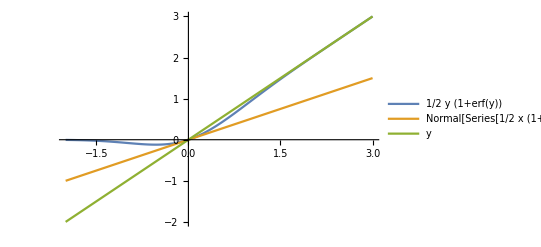

```mathematica
Plot[{y/2(1+Erf[y]),Normal[Series[x/2 (1+Erf[x]),{x,0,1}]]/.x->y,y},{y,-2,3},PlotLegends->"Expressions"]
```

```mathematica
AssetUpperBound[price_,K_,T_,r_]:=Exp[-r T] K*Exp[price/(K Exp[-r T])];
LogAssetUpperBound[price_,K_,T_,r_]:= price/(K Exp[-r T]) - r T + Log[K];
```

```mathematica
Manipulate[
Module[{x0=Log[fixS],x,newtonRoot,estimatedPrice},
x = LogAssetOfPrice[K,T,r,σ,K2,1,x0,nOrder];
newtonRoot = Timing[FindRoot[BSCallHandy[Exp[xx],K,T,r,σ]==K2,{xx,Log[fixS]}]];
estimatedPrice = BSCallHandy[Exp[x],K,T,r,σ];
{fixS,{K2,estimatedPrice},{Exp[x],x,newtonRoot}}
],
"target price, K2",
{{K2,20,""},0,100,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"strike, K",
{{K,100,""},0,150,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"volatility, σ",
{{σ,0.3,""},0.01,1,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"risk-free rate, r",
{{r,0.05,""},0.0,0.25,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"years to maturity, T",
{{T,1,""},0.1,3,0.25,Appearance->"Labeled", ImageSize-> Tiny},
"",
"truncated order, order",
{{nOrder,5,""},0,100,5,Appearance->"Labeled", ImageSize-> Tiny},
"",
"fixed S, fixS",
{{fixS,Exp[-r T] K*Exp[ K2/(K Exp[-r T])],""},1,600,5,Appearance->"Labeled", ImageSize-> Tiny},

ControlPlacement->Left,SaveDefinitions->True
]
```

### Conclusion

#### This is really a good initial guess of implied asset price.